Genez, Inc.
9617 Black Watch Court
Charlotte, NC 28277

February 17, 2020

To: Chief Scientist, Center for Bioinformatics
From: Aakriti Lakshmanan
Subj: Analysis of Microarray Data

## Summary and Introduction

### Abstract:

As requested in the Scope of Work, we have conducted an analysis on a specific mouse strain. The strain analyzed was the A/J strain. This analysis included a statistical analysis of data surround 17 other strains, as well as an in depth review of the selected strain.

### Introduction/Background Information:

Single nucleotide polymorphisms, otherwise known as SNPs, are a source of genetic differences between people. A SNP represents just a change in one nucleotide, and could just be a switch between two different ones. They are very common in our DNA, and can even be found in parts of DNA that doesn’t code for a gene. This means that scientists can use them as a marker and help locate other genes. When these mutations occur inside of a gene, they can either have no effect or direct impact the function of the gene. While most have no effect, there are some types that can help build resistance. SNPs can be passed down through families, and can be used to analyze the heritability of a disease or gene. [1]

	Gene expression is a measure of how well a gene is present in the phenotype. Gene expression is when the information stored in DNA is extracted and converted into code for proteins and other important molecules like functional RNA. All forms of life use gene expression in order to keep themselves alive. The code stored in our DNA is known as our genotype, which is the actual genes we carry. However, the process of gene expression allows for the genotype to be expressed physically, which creates the phenotype. Not all of the genes present in our genotype will be visible though the phenotype, since some genes may be recessive. The process by which gene expression occurs spans several steps, and begins with transcription. [2] This process creates different RNA sequences, which are known as transcripts. The transcript created is also dependent on factors like where in the body it is located and when the DNA replication process occurs. 
	
	A functional variant is a type of mutation that directly affects the function of a gene. Due to the repetitive nature of DNA, these variants are relatively rare. These are also the type of variants that lead to complex diseases. [3] Structural variants refers to the general variation found in chromosomes. They are similar to single nucleotide polymorphisms, but instead of just affecting one nucleotide, they affect a sequence that can be around 1 kb long. Another difference is that they are harder to detect. They also are one of the causes of genetic diseases. These variants can take various different styles, including inversion, insertions, deletions and duplications. [4] Another type of mutation is an index, where bases are deleted or inserted into the genome. [5] The protein coding sequence is the part of the gene that actually codes for protein, and is made up of codon. It is the part of the gene that is of most importance to scientists. [6]
	
	Substitutions are yet another mutation style. In this kind of mutation, a nucleotide is swapped out for another base. Since multiple codons can code for the same amino acids, this can sometimes lead to synonymous substitutions where the actual protein sequence is not affected. However, this isn’t always the case. In the case where the codons are changed to code for another amino acid, the sequence of proteins is changed. This is known and a non-synonymous substitution. Some codons are start and stop codons, and substitutions in these codons can cause a large effect. [7] When scientists want to resemble the natural world, they may end up studying wild-type organisms. these organisms have the phenotype of a species as natural as it appears in nature. The wild type has the highest gene frequency. [8] 

	Quantitative traits are affected by the interaction of multiple different genes. They are complex, and don’t act like regular Mendelian traits. This means that one gene isn’t enough to explain these traits. These types of of traits are actually much more common, and scientists continue to focus on how genetic variants affect these traits. [9] A quantitative trait locus, otherwise known as a QTL is an area that correlates with a quantitative trait. They correlate markers like SNPs with a physical trait, and can help narrow down where the actual genes are located. There can be multiple loci on different chromosomes, and the number and length of these focuses can reveal a lot about the complexity of the trait. [10] Phylogeny is a branch of science that focuses on relationships between species. It also focuses on evolution. [11]

## Methodology

For this study, data was collected from databases such as Jackson Laboratory and Mouse Genome Database. The following analyses were conducted:

A description of the gene

An analysis of the phenotype of the gene

An analysis of the SNPs and variations of the gene

A statistical analysis of data from NCSSM’s database

## Results

### Description:

The A/J strain was first created in 1921, with a cross between a Cold Spring Harbor and a Bagg albino mice. They are mainly used for cancer and immunology research, and as such have garnered a large importance in the field of mouse genetics. A few of the diseases that this strain of mice is susceptible to cleft palate, and readily develops begin lung tumors when exposed to carcinogens. This allows ancients easy access to cancerous tissues, and allows them to test treatment methods. [12] This strain of mice also experiences late onset muscular dystrophy, due to an insertion in the dysferlin gene.  The strain has an albino coat, with a smaller brain and kidney.

### Phenotype Overview:

As shown in the below image, the A/J strain has many different mutations that affect the mouse’s phenotype. The first category of the phenotype that was affected was behavior/neurological. This is actually impacted by a mutation in the dysferlin gene, as mentioned above. This can cause abnormal strength, and limb grasping. On the cellular level, this mutation can also cause skeletal muscle fiber necrosis, which leads to muscular dystrophy later on in the mice’s life span. There are many other genes that have either structural variation or SNPs in the A/J strain, which causes the differenced in the following pheotypes. Some of the effects of these mutations include increased/decreased susceptibility to bacterial infection and ovary inflammation. [13]

### Modeled Diseases:

#### Tumors:

This mice actually has a high susceptibility to developing lung tumors, even with a low exposure to carcinogens. The main reason that this occurs is due to a polymorphism in the apoptosis inhibitory protein 5 gene, otherwise known as the Naip5 gene. As shown in the Mouse Phenome database, there are 70 SNPs that A/J has on this gene that the regular black 6 mouse strain does not have. A few of these SNPs are detailed in the image below. [14]

The actual function variant that causes this difference is shown below. It is located on chromosome 13, with the given base pair location. The “I” in the third column means that there is an intron-variant. Given that the intron is a codon that actually codes for a protein, this mutation is ultimately what affects the ability of this gene to function as normal.

-Graphics-

Since this gene regularly inhibits apoptosis, which is the death of cells, the mutation in the A/J strain causes an increased susceptibility to tumors.

#### Muscular Dystrophy:

This mice strain also has a tendency to develop muscular dystrophy 4-5 months after being born. This is known as late onset muscular dystrophy, and can hinder the use of this strain for long term experiments. The cause of this condition is a insertion on intron 4 of the dysferlin gene. This mutation caused the wrong amino acid to be produced, which abolished the protien and hindered the ability of the gene to perform it’s function. However, this is also useful because this strain of mice can actually serve as a model for the human disease “autosomal recessive limb-girdle muscular dystrophy type 2B.”

#### Cleft Palate:

This mice strain also has an increased susceptibility to developing cleft palate when given cortisone. This is due to a mutation in the Wnt9b, or cleft lip 1 gene. The phenotype of this gene is cleft palate. Since the mice is very sensitive to cortisone, scientists are able to study the cleft palate in more detail. [14]

### Statistical Analysis:

Data describing different strains of mice was imported from a server located at NCSSM, and the raw data is as follows.

```mathematica
data=Import["/Users/aakritilakshmanan/Downloads/MouseSequences2.csv"];
Grid[data,Frame-> All]
```

Strain | Gb of mapped data | % of genome inaccessible | SNPs | Indels | Structural Variants
C57BL/6NJ | 77.29 | 13.21 | 9844 | 22228 | 431
129Si/SvlmJ | 27.91 | 15.3 | 4458004 | 886136 | 29153
129S5SvEv | 50.27 | 15.17 | 4383799 | 810310 | 25340
129P2/Ola | 115.52 | 14.47 | 4694529 | 1028629 | 32227
A/J | 70.39 | 15.9 | 4198324 | 823688 | 28691
AKR/J | 107.16 | 14.86 | 4331384 | 966002 | 30742
BALB/cJ | 65.72 | 15.09 | 3920925 | 831193 | 25702
C3H/HeJ | 92.81 | 15.09 | 4403599 | 949206 | 28532
CBA/J | 77.43 | 14.79 | 4511278 | 929860 | 28183
DBA/2J | 65.11 | 15.09 | 4468071 | 868611 | 28346
LP/J | 73.03 | 15.29 | 4701445 | 947614 | 30024
NOS/ShiLtJ | 75.88 | 17.3 | 4323530 | 797086 | 30605
NZO/HILtJ | 45.68 | 16.06 | 4492372 | 806511 | 25125
PWK/PhJ | 66.99 | 19.26 | 17202436 | 2634885 | 90125
CAST/EiJ | 64.84 | 19.18 | 17673726 | 2727089 | 86322
WSB/EiJ | 48.19 | 16.23 | 6045573 | 1197006 | 35066
SPRET/EiJ | 70.41 | 23.36 | 35441735 | 4456243 | 157306

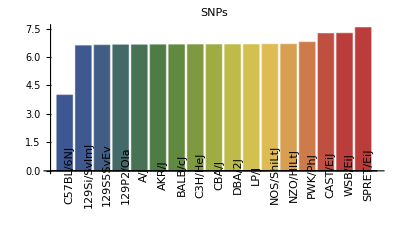

```mathematica
newData=Delete[data,1];
{strain, gb ,genomeinaccessible, SNPs, Indels, variants}=Transpose[newData];
log10SNPs=N[Log10[SNPs]];
resultsSNP=Table[
{
newData[[row,1]],
N[Log10[newData[[row,4]]]]
},
{row,1,Length[newData]}
];
Grid[resultsSNP,Frame->All];
BarChart[Sort[log10SNPs], ChartLabels->Placed[strain,Below,Rotate[#,90 Degree] &], ChartStyle->"DarkRainbow",PlotLabel->HoldForm[SNPs],LabelStyle->{GrayLevel[0]}]
```

This bar chart provides a clear view into the amount of SNPs that each strain has. C57BL/6NJ has a lower than average amount of SNPs, which makes sense as this strain is the most general and isn’t as specialized for one purpose when compared to the other strains. Most strains, including A/J, had a similar amount of SNPs. SPRET/EJ had a higher than average amount of SNPs. This is due to the fact that this strain is a wild-type strain, so it has a high gene frequency.

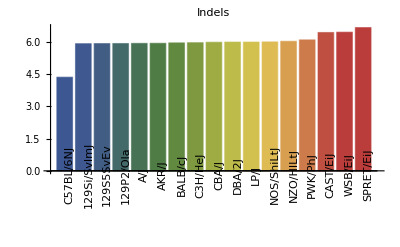

```mathematica
log10Indels=N[Log10[Indels]];
resultsIndels=Table[
{
newData[[row,1]],
N[Log10[newData[[row,5]]]]
},
{row,1,Length[newData]}
];
Grid[resultsIndels,Frame->All];
BarChart[Sort[log10Indels], ChartLabels->Placed[strain,Below,Rotate[#,90 Degree] &], ChartStyle->"DarkRainbow",PlotLabel->HoldForm[Indels],LabelStyle->{GrayLevel[0]}]
```

This bar chart follows the same trend, with the wild-type strain having the most insertions and deletions and the black mice having the least. CAST/EJ is also another wild-type strain.

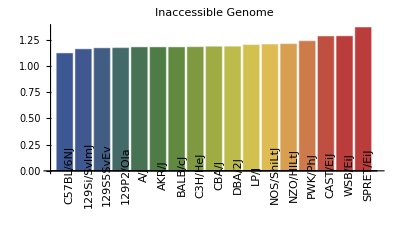

```mathematica
log10genomeinaccessible=N[Log10[genomeinaccessible]];
resultsgenomeinaccessible=Table[
{
newData[[row,1]],
N[Log10[newData[[row,5]]]]
},
{row,1,Length[newData]}
];
Grid[resultsgenomeinaccessible,Frame->All];
BarChart[Sort[log10genomeinaccessible], ChartLabels->Placed[strain,Below,Rotate[#,90 Degree] &], ChartStyle->"DarkRainbow",PlotLabel->HoldForm["Inaccessible Genome"],LabelStyle->{GrayLevel[0]}]
```

This graph continues the trend shown in the other bar charts. As shown, the wild-type mouse strains have a higher than average percentage that is still not accessible. The other strains, including the black 6 strain, all have similar levels of inaccessible genome. However, as time continues, this amount will only continue to go down.

I certify that this work was completed by me on February 17, 2020.  All references and resources are cited.  Assistance was provided by NAME OF PERSON(S) (if any)
  Electronic signature: -Graphics-

References:

1. Home, Genetics. “What Are Single Nucleotide Polymorphisms (SNPs)?” Genetics Home Reference, https://ghr.nlm.nih.gov/primer/genomicresearch/snp. Accessed 18 Feb. 2020.
2. Wikipedia. “Gene Expression.” Wikipedia , https://en.wikipedia.org/wiki/Gene_expression. Accessed 29 Jan. 2020.
3. ---. “Rare Functional Variant.” Wikipedia, 19 Feb. 2020, https://en.wikipedia.org/wiki/Rare_functional_variant.
4. ---. “Structural Variation.” Wikipedia, 19 Feb. 2020, https://en.wikipedia.org/wiki/Structural_variation.
5. ---. “Indel.” Wikipedia, 19 Feb. 2020, https://en.wikipedia.org/wiki/Indel.
6. Wikipedia. “Coding Region.” Wikipedia, 18 Feb. 2020, https://en.wikipedia.org/wiki/Coding_region.
7. ---. “Synonymous Substitution.” Wikipedia, 18 Feb. 2020, https://en.wikipedia.org/wiki/Synonymous_substitution.
8. ---. “Wild Type.” Wikipedia, 18 Feb. 2020, https://en.wikipedia.org/wiki/Wild_type.
9. ---. “Complex Traits.” Wikipedia, 19 Feb. 2020, https://en.wikipedia.org/wiki/Complex_traits.
10. ---. “Quantitative Trait Locus.” Wikipedia, 18 Feb. 2020, https://en.wikipedia.org/wiki/Quantitative_trait_locus.
11. ---. “Phylogenetics.” Wikipedia, 18 Feb. 2020, https://en.wikipedia.org/wiki/Phylogenetics.
12. 000646 - A/J. https://www.jax.org/strain/000646. Accessed 18 Feb. 2020.
13. A/J Strain Detail MGI Mouse MGI:2159747. http://www.informatics.jax.org/strain/MGI:2159747. Accessed 18 Feb. 2020.
14. “Retrieval.” Jackson Lab, https://phenome.jax.org/snp/retrieval. Accessed 18 Feb. 2020.